```mathematica
Exit[]
```

```mathematica
nn=26;u0=Table[Sin[i 2 Pi 10 /nn],{i,1,nn}]//N
```

{0.663123,-0.992709,0.822984,-0.239316,-0.464723,0.935016,-0.935016,0.464723,0.239316,-0.822984,0.992709,-0.663123,0.,0.663123,-0.992709,0.822984,-0.239316,-0.464723,0.935016,-0.935016,0.464723,0.239316,-0.822984,0.992709,-0.663123,0.}

```mathematica
c=Table[Sum[Exp[-I 2 Pi n m/nn]/nn u0[[n]],{n,1,nn}],{m,1,nn}]//N
c=Table[I DiscreteDelta[i-2],{i,1,nn}]//N
u[t_]:=Simplify[Table[Sum[c[[m]]*Exp[I ( 2 Pi m n/nn-w[m] t)],{m,1,nn}],{n,1,nn}]]
```

{0.-1.9082×10^-17 ⅈ,0.+4.68375×10^-17 ⅈ,0.-6.93889×10^-18 ⅈ,0.+1.38778×10^-17 ⅈ,1.73472×10^-18+0. ⅈ,9.54098×10^-18-2.77556×10^-17 ⅈ,1.30104×10^-18+0. ⅈ,-6.93889×10^-18+1.38778×10^-17 ⅈ,-1.04083×10^-17-3.46945×10^-18 ⅈ,0.-0.5 ⅈ,1.38778×10^-17-8.67362×10^-18 ⅈ,1.73472×10^-17+3.90313×10^-17 ⅈ,0.,1.73472×10^-17-3.90313×10^-17 ⅈ,1.38778×10^-17+8.67362×10^-18 ⅈ,0.+0.5 ⅈ,-1.04083×10^-17+3.46945×10^-18 ⅈ,-6.93889×10^-18-1.38778×10^-17 ⅈ,1.30104×10^-18+0. ⅈ,9.54098×10^-18+2.77556×10^-17 ⅈ,1.73472×10^-18+0. ⅈ,0.-1.38778×10^-17 ⅈ,0.+6.93889×10^-18 ⅈ,0.-4.68375×10^-17 ⅈ,0.+1.9082×10^-17 ⅈ,0.}

{0.,0.+1. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
w[m_]:=2*0.01 Abs[Sin[Pi m/nn]];
```

```mathematica
p=8;c=Table[I DiscreteDelta[i-p],{i,1,nn}]//N
u[t_]:=Simplify[Table[Sum[c[[m]]*Exp[I ( 2 Pi m n/nn-w[m] t)],{m,1,nn}],{n,1,nn}]]
Animate[ListPlot[{Re[u[t]]},Joined->True,PlotRange->{-1,1}],{t,0,2 Pi/w[p]//N}]
```

{0.,0.,0.,0.,0.,0.,0.,0.+1. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

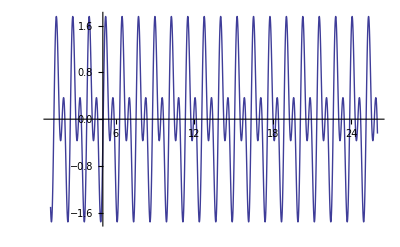

```mathematica
Plot[Sin[5x]+Sin[10x],{x,1,nn}]
```

```mathematica
,
```

```mathematica
u[0]//N
```

{1.30515×10^-17-1.79638×10^-17 ⅈ,0.,1.30515×10^-17-1.79638×10^-17 ⅈ,0.,1.,0.,1.30515×10^-17-1.79638×10^-17 ⅈ,0.,1.30515×10^-17-1.79638×10^-17 ⅈ,0.}